```mathematica
ScreeSSA[Serie_,L_]:=(
X=Partition[Serie,L,1];
r=MatrixRank[X];
σ=SingularValueList[N[X],r];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
;)

PartialScreeSSA[Serie_,L_,rMax_]:=(
X=Partition[Serie,L,1];
Σ=SingularValueList[N[X],rMax][[2]];
σ=Table[Σ[[k,k]],{k,1,rMax}];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
;)

CompleteSSA[Serie_,L_]:=(
Dim=Dimensions[Serie][[1]];
(* SVD *)
X=Partition[Serie,L,1];
K=Dimensions[X][[1]];
r=MatrixRank[X];
{U,Σ,V}=SingularValueDecomposition[N[X],r];
(* scree diagram *)
σ=Table[Σ[[k,k]],{k,1,r}];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
(* matrices elementales *)
For[k=1,k≤r,k++,{
XX[k]=σ[[k]]*Outer[Times,Transpose[U][[k]],Transpose[V][[k]]]; 
XXX[k]=Transpose[Table[XX[k][[All,n]],{n,L,1,-1}]]
}];
(* Modos reconstruidos *)
For[k=1,k≤r,k++,{
g[k]=Table[
Mean[Diagonal[XXX[k],i]]
,{i,Min[K-1,L-1],-Max[K-1,L-1],-1}]
}];
(* wMatriz *)
w={};
LL=Min[L,K];
KK=Max[L,K];
For[i=1,i≤LL,i++,{
AppendTo[w,i]
}]
For[i=LL+1,i≤KK,i++,{
AppendTo[w,LL]
}]
For[i=KK+1,i≤Dim,i++,{
AppendTo[w,Dim-i]
}];
kMin=kkMin=1;kMax=kkMax=20;
wMatriz=Table[Total[w*g[k]*g[kk]]/(Sqrt[Total[w*g[k]^2]]*Sqrt[Total[w*g[kk]^2]]),{k,kMin,kMax},{kk,kkMin,kkMax}];
;)

PartialSSA[Serie_,L_,rMax_,gYesNo_,wYesNo_]:=(
Dim=Dimensions[Serie][[1]];
(* SVD *)
X=Partition[Serie,L,1];
K=Dimensions[X][[1]];
r=MatrixRank[X];
{U,Σ,V}=SingularValueDecomposition[N[X],rMax];
(* scree diagram *)
σ=Table[Σ[[k,k]],{k,1,rMax}];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
If[gYesNo=="Yes",{
(* matrices elementales *)
For[k=1,k≤rMax,k++,{
XX[k]=σ[[k]]*Outer[Times,Transpose[U][[k]],Transpose[V][[k]]]; 
XXX[k]=Transpose[Table[XX[k][[All,n]],{n,L,1,-1}]]
}];
(* Modos reconstruidos *)
For[k=1,k≤rMax,k++,{
g[k]=Table[
Mean[Diagonal[XXX[k],i]]
,{i,Min[K-1,L-1],-Max[K-1,L-1],-1}]
}];
}];
If[wYesNo=="Yes",{
(* wMatriz *)
w={};
LL=Min[L,K];
KK=Max[L,K];
For[i=1,i≤LL,i++,{
AppendTo[w,i]
}]
For[i=LL+1,i≤KK,i++,{
AppendTo[w,LL]
}]
For[i=KK+1,i≤Dim,i++,{
AppendTo[w,Dim-i]
}];
kMin=kkMin=1;kMax=kkMax=Min[20,rMax];
wMatriz=Table[Total[w*g[k]*g[kk]]/(Sqrt[Total[w*g[k]^2]]*Sqrt[Total[w*g[kk]^2]]),{k,kMin,kMax},{kk,kkMin,kkMax}];
}]
;)

SetDirectory["C:\Users\sqrf\Documents\Carbono Negro"]


Semana = 14


DatTemp=Import["2015-CCA-Temp(by weeks).xlsx",{"Data",1,All, Semana}];
DatosT =Transpose[Table[DatTemp, {1}]]

Dat=Import["2015-CCA-O3(by weeks).xlsx",{"Data",1,All, Semana+1}];
Datos =Transpose[Table[Dat, {1}]]

DatNO=Import["2015-CCA-NO(by weeks).xlsx",{"Data",1,All, Semana+1}];
DatosNO =Transpose[Table[DatNO, {1}]]

DatNO2=Import["2015-CCA-NO2(by weeks).xlsx",{"Data",1,All, Semana+1}];
DatosNO2 =Transpose[Table[DatNO2, {1}]]

DatNOx=Import["2015-CCA-NOx(by weeks).xlsx",{"Data",1,All, Semana+1}];
DatosNOx =Transpose[Table[DatNOx, {1}]]

DatCO=Import["2015-CCA-CO(by weeks).xlsx",{"Data",1,All, Semana+1}];
DatosCO =Transpose[Table[DatCO, {1}]]

DatPM25=Import["2015-CCA-PM2.5(by weeks).xlsx",{"Data",1,All, Semana+1}];
DatosPM25 =Transpose[Table[DatPM25, {1}]]

DatSO2=Import["2015-CCA-SO2(by weeks).xlsx",{"Data",1,All, Semana+1}];
DatosSO2 =Transpose[Table[DatSO2, {1}]]

DatBC=Import["MatrixBC.xlsx",{"Data",1,All, Semana}];
DatosBC =Transpose[Table[DatBC, {1}]]

(*{"Data",# of sheet(s),# of row(s),# of column(s)}
*)
{M,T}=Dimensions[Datos]
{M,T}=Dimensions[DatosNO]
{M,T}=Dimensions[DatosNO2]
{M,T}=Dimensions[DatosNOx]
{M,T}=Dimensions[DatosCO]
{M,T}=Dimensions[DatosSO2]
{M,T}=Dimensions[DatosPM25]
{M,T}=Dimensions[DatosBC]



SerieT=Flatten[Join[Table[DatosT[[All,t]],{t,1,T}]]];
Serie=Flatten[Join[Table[Datos[[All,t]],{t,1,T}]]];
SerieNO=Flatten[Join[Table[DatosNO[[All,t]],{t,1,T}]]];
SerieNO2=Flatten[Join[Table[DatosNO2[[All,t]],{t,1,T}]]];
SerieNOx=Flatten[Join[Table[DatosNOx[[All,t]],{t,1,T}]]];
SerieCO=Flatten[Join[Table[DatosCO[[All,t]],{t,1,T}]]];
SeriePM25=Flatten[Join[Table[DatosPM25[[All,t]],{t,1,T}]]];
SerieSO2=Flatten[Join[Table[DatosSO2[[All,t]],{t,1,T}]]];
SerieBC=Flatten[Join[Table[DatosBC[[All,t]],{t,1,T}]]];
```

C:\Users\sqrf\Documents\Carbono Negro

14

{{13.},{13.1},{13.1},{13.1},{13.1},{13.1},{13.},{13.1},{13.1},{13.1},{13.},{13.},{12.9},{12.8},{12.7},{12.7},{13.3},{14.1},{15.4},{16.2},{16.7},{17.5},{18.3},{19.2},{19.9},{20.},{20.2},{20.6},{21.},{21.2},{21.8},{21.5},{21.1},{20.9},{20.2},{19.9},{19.7},{19.9},{19.2},{16.7},{16.4},{16.7},{16.5},{16.4},{16.3},{16.3},{16.2},{15.7},{15.4},{15.1},{14.7},{14.6},{14.3},{14.3},{13.9},{13.3},{12.9},{13.1},{13.2},{13.3},{13.4},{13.4},{13.4},{13.8},{14.1},{15.1},{16.},{16.7},{17.3},{18.3},{19.2},{19.8},{20.8},{21.7},{21.8},{22.9},{23.2},{22.7},{22.6},{22.9},{22.9},{23.2},{23.4},{23.1},{22.6},{21.9},{20.6},{19.6},{18.7},{16.4},{15.4},{15.6},{15.7},{16.2},{16.4},{16.1},{15.7},{15.8},{15.8},{15.7},{15.5},{14.9},{14.7},{14.7},{14.7},{14.6},{14.3},{14.1},{13.9},{13.8},{13.8},{14.1},{14.7},{15.3},{15.7},{16.6},{17.2},{18.2},{18.9},{20.1},{20.4},{21.},{21.3},{21.9},{22.1},{21.9},{22.},{22.6},{22.9},{22.9},{22.9},{22.6},{21.8},{20.6},{20.2},{19.2},{18.7},{18.6},{18.3},{17.8},{17.4},{17.2},{16.9},{16.8},{16.4},{16.4},{16.5},{16.3},{15.9},{15.2},{15.},{15.},{15.},{14.9},{14.8},{14.8},{14.6},{14.4},{14.4},{14.7},{15.4},{16.2},{17.2},{18.2},{19.},{19.9},{21.1},{22.1},{22.7},{23.4},{24.1},{24.4},{24.5},{25.1},{25.2},{24.3},{24.4},{23.6},{23.4},{23.3},{23.3},{22.8},{21.9},{20.9},{20.},{17.3},{15.6},{15.8},{16.},{16.3},{16.3},{16.4},{16.2},{15.9},{15.8},{15.5},{15.2},{14.7},{14.3},{14.4},{14.2},{14.1},{14.1},{13.8},{14.1},{14.2},{14.3},{15.1},{15.8},{16.6},{17.1},{17.3},{17.7},{18.3},{18.7},{19.1},{19.9},{20.7},{20.9},{21.9},{22.2},{21.3},{20.7},{21.3},{21.8},{21.9},{21.6},{21.2},{21.1},{20.7},{20.4},{20.3},{19.9},{18.9},{18.3},{18.},{17.8},{17.7},{17.6},{17.6},{17.5},{17.3},{16.4},{15.5},{15.3},{15.2},{15.2},{15.2},{15.4},{15.6},{15.6},{15.7},{15.7},{15.8},{15.8},{15.7},{15.7},{16.1},{16.9},{17.4},{17.8},{18.9},{20.2},{21.1},{21.6},{22.2},{22.7},{21.6},{16.1},{15.2},{16.8},{18.4},{18.3},{17.8},{18.3},{18.1},{16.9},{16.7},{16.1},{15.5},{15.2},{14.8},{14.4},{14.4},{14.5},{14.6},{14.7},{14.6},{14.7},{14.8},{14.8},{14.7},{14.8},{14.7},{14.6},{14.6},{14.6},{14.4},{14.4},{14.4},{14.4},{14.4},{14.4},{14.8},{15.1},{15.6},{16.2},{16.7},{17.6},{18.1},{18.9},{20.7},{21.2},{21.8},{22.4},{23.},{23.3},{23.8},{23.7},{24.7},{24.8},{25.3},{25.},{25.1},{25.1},{24.8},{24.2},{23.1},{21.4},{20.5},{19.9},{19.4},{18.8},{18.2},{17.7},{16.8}}

{{1.5},{7.5},{27.5},{44.},{15.},{24.},{11.5},{1.},{22.},{0.},{9.5},{15.},{1.},{6.},{43.},{76.},{90.5},{68.5},{59.5},{40.},{1.5},{4.5},{1.},{17.5},{1.},{5.5},{27.},{46.5},{51.5},{35.5},{28.5},{1.},{6.},{12.5},{6.5},{1.},{2.5},{9.},{42.5},{0.},{45.},{37.5},{19.},{19.},{1.5},{11.},{8.},{1.},{4.5},{9.5},{44.5},{66.},{60.},{51.},{46.5},{35.5},{8.},{8.},{20.},{11.},{1.5},{14.5},{42.},{40.5},{32.},{29.},{18.},{19.5},{3.},{27.5},{6.5},{7.},{1.},{20.5},{42.},{70.5},{46.5},{19.},{10.},{15.5},{10.},{7.5},{19.5},{10.},{1.5},{26.},{60.},{84.},{91.5},{80.5},{52.},{54.},{39.5},{0.},{14.5},{4.},{2.},{18.5},{79.},{83.},{87.},{60.5},{47.5},{3.},{24.},{18.},{28.5},{9.},{1.5},{3.},{56.},{85.5},{55.5},{80.5},{35.},{14.},{14.5},{11.5},{4.},{9.},{3.5},{20.5},{52.},{91.5},{68.},{25.5},{38.},{24.},{18.5},{4.},{31.5},{3.},{7.},{26.5},{59.5},{109.5},{90.},{39.},{26.},{14.5},{18.5},{22.},{9.},{3.5},{3.},{17.5},{54.},{0.},{160.5},{80.5},{34.},{17.5},{11.},{10.},{3.5},{4.},{5.},{10.},{79.5},{68.},{72.},{40.5},{26.},{15.},{17.},{3.5},{11.},{6.},{3.5},{8.},{42.},{77.5},{99.},{41.},{37.5},{30.5},{5.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{4.},{18.},{45.},{79.5},{109.5},{51.5},{23.5},{17.},{8.},{25.5},{1.},{1.5},{3.},{21.},{37.},{56.5},{103.},{61.},{48.},{3.},{4.},{0.},{27.5},{1.},{0.},{0.},{43.},{46.5},{67.},{50.5},{36.},{10.5},{6.},{39.5},{16.},{1.5},{1.5},{19.},{45.},{91.5},{124.},{39.5},{21.},{28.},{14.5},{16.},{2.5},{1.5},{1.5},{16.},{47.},{28.},{72.5},{78.},{19.5},{16.},{1.},{11.},{19.5},{11.},{4.5},{24.5},{53.5},{118.5},{81.5},{45.},{19.},{24.5},{15.},{11.},{3.},{2.5},{2.},{5.},{37.},{24.5},{35.},{42.5},{17.},{3.5},{0.},{11.5},{0.5},{4.},{0.5},{8.},{45.5},{22.5},{16.5},{34.},{3.},{18.5},{6.5},{0.},{3.},{13.},{1.},{8.5},{42.},{67.5},{30.},{9.5},{13.},{10.5},{1.},{1.},{16.},{1.},{11.5},{2.5},{37.5},{75.},{112.},{17.},{22.5},{13.5},{1.5},{2.},{11.5},{1.5},{2.5},{6.},{20.5},{61.5},{62.5},{90.5},{36.5},{27.},{2.},{2.5},{2.},{3.5},{1.5},{6.5},{49.5},{71.},{64.5},{26.5},{38.},{28.5},{22.},{7.5},{6.5},{1.}}

{{30.5},{75.5},{7.},{0.},{0.},{0.},{0.},{47.5},{1.},{0.},{1.5},{2.},{89.5},{141.5},{19.5},{6.},{3.},{2.5},{1.5},{2.},{25.5},{3.5},{9.5},{1.},{122.5},{136.5},{36.5},{24.5},{2.},{1.},{1.5},{45.},{6.5},{1.},{6.},{17.5},{103.},{84.},{29.5},{0.},{14.},{9.},{3.},{1.},{38.5},{6.},{2.5},{30.},{21.},{97.5},{19.},{1.5},{2.5},{1.5},{1.},{1.},{5.5},{2.5},{1.},{2.},{48.5},{33.},{18.},{7.5},{9.},{8.},{9.5},{4.5},{4.5},{1.},{6.},{2.5},{97.5},{32.},{9.5},{4.5},{4.5},{7.},{13.},{3.},{3.},{2.},{1.},{3.},{44.5},{23.5},{4.},{4.},{1.5},{2.5},{2.},{1.5},{0.5},{0.},{1.5},{8.},{98.5},{65.},{7.},{2.},{1.},{3.},{1.},{21.},{1.5},{1.5},{1.},{23.5},{159.5},{47.},{8.5},{2.5},{1.5},{1.},{2.},{4.},{2.5},{1.5},{5.},{2.5},{0.},{33.5},{20.},{5.},{2.},{9.},{1.},{2.},{1.5},{11.},{1.},{6.5},{19.},{29.},{11.},{3.5},{2.},{2.5},{1.},{1.},{1.5},{1.},{1.5},{13.},{31.5},{14.},{11.},{0.},{1.5},{2.},{2.},{2.},{1.},{1.5},{5.},{9.},{38.5},{24.5},{7.},{18.5},{2.},{3.},{2.},{8.5},{1.5},{6.},{2.5},{24.5},{44.},{50.5},{13.},{4.},{2.},{5.5},{1.},{1.},{3.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{44.5},{24.5},{14.},{6.},{2.},{2.},{2.5},{1.5},{7.},{1.},{3.},{7.},{26.5},{23.5},{7.5},{4.5},{1.5},{1.},{1.},{15.},{14.5},{0.},{0.5},{0.},{0.},{0.},{8.},{2.5},{1.},{2.},{0.},{1.5},{4.5},{0.5},{1.},{29.5},{44.5},{14.},{7.5},{5.},{1.},{3.},{5.},{0.5},{1.},{0.5},{8.},{20.},{49.5},{42.5},{5.},{2.},{3.},{1.},{0.},{2.},{27.5},{0.},{0.},{1.5},{23.5},{24.},{18.5},{1.},{1.5},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{52.},{31.},{13.5},{7.5},{3.},{4.},{4.5},{9.5},{0.},{3.},{16.},{1.5},{114.5},{53.5},{14.5},{7.5},{6.},{2.},{11.},{2.},{3.5},{0.},{2.5},{0.5},{68.},{77.5},{25.5},{6.},{2.},{4.5},{1.5},{2.5},{89.},{49.},{1.},{23.},{1.5},{53.},{24.5},{5.},{3.},{13.5},{1.5},{2.5},{40.},{59.5},{1.},{10.5},{14.5},{15.5},{36.},{5.5},{3.},{2.5},{3.},{1.},{64.5},{69.},{18.5},{19.},{76.},{79.},{14.},{6.},{8.5},{2.},{2.},{1.5},{5.},{2.},{5.},{36.}}

{{27.},{38.},{14.},{0.},{0.},{0.},{0.},{47.5},{27.},{0.},{19.5},{17.5},{32.},{51.5},{39.},{30.5},{19.},{26.5},{60.},{14.5},{35.},{23.5},{29.5},{16.5},{24.},{49.5},{47.5},{63.5},{8.},{5.5},{11.},{33.5},{38.5},{20.5},{26.},{28.5},{29.5},{42.5},{56.5},{0.},{64.5},{52.},{27.5},{14.},{45.},{35.},{29.},{30.5},{30.},{49.5},{43.},{8.5},{12.},{10.},{20.5},{34.},{43.},{36.},{15.5},{17.},{28.},{30.5},{36.5},{14.5},{11.},{15.5},{25.5},{11.5},{25.5},{6.},{19.},{16.},{25.},{35.},{22.5},{25.5},{13.},{22.5},{22.5},{22.5},{27.5},{24.},{13.},{24.},{21.},{25.5},{13.5},{20.5},{10.5},{21.5},{51.},{26.},{11.5},{0.},{17.},{22.},{34.},{65.},{30.5},{13.},{9.5},{16.},{26.5},{42.5},{16.5},{26.5},{15.5},{30.},{37.},{36.},{25.},{17.},{12.5},{13.5},{23.5},{47.},{22.},{11.},{14.},{23.},{0.},{42.},{50.},{30.5},{18.},{35.},{21.5},{26.},{22.5},{21.},{7.5},{15.5},{28.},{38.5},{35.5},{28.},{19.},{27.},{23.5},{23.5},{20.},{13.},{18.5},{19.5},{30.5},{25.},{31.},{0.},{26.},{17.},{28.5},{18.5},{14.5},{20.},{26.},{21.5},{24.},{26.},{32.},{51.},{13.5},{15.5},{33.},{40.5},{25.5},{45.},{24.5},{23.5},{24.5},{38.},{28.5},{17.5},{24.},{24.},{20.},{24.5},{23.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{28.},{30.5},{30.5},{27.},{18.5},{15.},{29.},{27.5},{26.},{12.},{14.5},{27.},{24.5},{27.5},{16.5},{21.},{20.},{12.},{14.},{47.5},{31.},{0.},{18.},{0.},{0.},{0.},{21.},{10.5},{19.5},{20.5},{15.},{33.},{32.},{11.},{26.},{28.},{22.},{19.},{17.5},{33.},{23.5},{15.5},{27.5},{20.5},{30.},{24.},{24.},{22.},{31.},{33.},{16.5},{13.5},{22.},{20.},{0.},{21.5},{33.},{14.5},{14.},{20.},{39.5},{27.},{47.5},{17.},{19.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{30.5},{24.5},{25.5},{17.5},{13.5},{27.5},{28.},{35.},{0.},{8.},{9.5},{20.5},{18.5},{49.5},{36.5},{10.5},{9.5},{18.},{18.},{40.5},{31.5},{0.},{23.5},{12.5},{13.},{38.5},{51.5},{26.},{18.},{24.},{29.5},{39.},{36.},{33.},{13.},{22.},{15.5},{31.},{42.5},{22.5},{33.},{25.5},{41.5},{49.},{62.5},{50.5},{17.5},{29.},{30.5},{28.},{39.5},{23.5},{32.5},{47.5},{37.},{19.5},{20.5},{26.5},{24.5},{22.5},{31.},{39.5},{33.5},{29.},{49.},{23.5},{49.},{37.},{17.5},{20.5},{26.},{24.}}

{{57.},{113.5},{21.5},{0.},{0.},{0.},{0.},{95.},{28.},{0.},{21.},{19.5},{121.5},{193.},{58.5},{36.5},{21.5},{28.5},{62.},{15.5},{60.5},{27.},{39.},{17.5},{147.5},{185.5},{84.},{88.},{10.},{6.5},{12.5},{78.5},{45.5},{21.5},{32.5},{46.},{132.5},{126.5},{85.5},{0.},{79.},{60.5},{30.5},{15.},{84.},{41.},{32.},{60.5},{51.5},{147.5},{63.},{10.5},{14.5},{12.},{22.},{35.},{48.5},{38.},{16.5},{19.},{76.5},{63.5},{54.},{21.5},{20.},{24.},{35.},{16.5},{30.},{6.5},{25.},{18.5},{123.5},{66.5},{31.5},{30.},{17.5},{29.},{35.5},{24.5},{30.5},{26.},{14.},{27.},{66.},{49.},{17.5},{24.5},{12.},{24.},{53.},{27.5},{11.5},{0.},{18.},{30.},{132.5},{130.5},{36.5},{14.5},{10.5},{19.5},{27.5},{63.5},{18.},{28.},{16.5},{54.},{197.},{83.},{34.},{19.5},{14.},{14.5},{25.},{51.5},{25.5},{12.5},{18.5},{26.},{0.},{75.5},{70.},{35.5},{20.5},{44.},{22.5},{28.5},{24.},{32.},{8.},{22.},{47.},{67.5},{47.},{31.5},{21.},{29.5},{25.5},{25.},{21.5},{14.},{20.},{32.5},{61.5},{39.},{42.},{0.},{27.5},{19.},{30.5},{20.},{16.},{22.},{31.},{30.5},{62.5},{50.5},{40.},{69.5},{15.},{18.5},{35.},{49.5},{27.},{51.5},{26.5},{48.},{68.5},{88.5},{41.5},{21.5},{26.},{29.5},{20.5},{25.5},{26.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{73.},{55.},{44.},{33.},{20.5},{17.},{32.},{29.5},{33.5},{13.},{17.},{34.},{51.},{50.5},{24.5},{25.5},{22.},{13.},{15.},{62.5},{46.5},{0.},{18.},{0.},{0.},{0.},{29.},{13.5},{20.5},{23.},{15.},{34.5},{36.5},{11.},{27.},{57.5},{66.5},{33.5},{24.5},{37.5},{24.5},{18.5},{32.5},{21.},{31.},{24.5},{31.5},{42.},{80.},{76.},{21.5},{15.5},{25.},{20.5},{0.},{23.},{61.5},{15.},{14.},{21.5},{63.},{51.},{66.5},{18.},{20.5},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{81.5},{55.5},{39.},{25.},{17.5},{31.},{32.5},{44.5},{0.},{11.},{25.},{22.5},{133.},{103.},{51.},{17.5},{15.5},{19.5},{29.5},{42.5},{35.5},{0.},{26.},{13.5},{80.5},{116.5},{77.5},{32.},{20.5},{28.},{31.},{41.5},{125.},{82.},{14.},{44.5},{17.},{84.5},{67.},{28.},{36.},{39.},{42.5},{51.5},{102.5},{110.},{18.5},{40.},{45.},{43.},{75.5},{29.5},{35.5},{50.},{40.},{20.5},{84.5},{95.5},{43.5},{41.5},{107.},{118.5},{47.5},{35.},{57.},{26.},{50.5},{39.},{22.},{22.5},{30.5},{60.}}

{{1.9},{1.85},{0.75},{0.8},{0.8},{0.7},{0.55},{1.35},{0.6},{0.},{0.45},{0.4},{1.25},{2.45},{1.1},{0.8},{0.6},{0.6},{1.3},{0.35},{0.8},{0.45},{0.75},{0.45},{1.5},{2.15},{1.2},{1.25},{0.2},{0.2},{0.3},{1.15},{0.65},{0.35},{0.45},{0.6},{1.1},{1.95},{1.35},{0.},{1.25},{1.},{0.6},{0.3},{1.1},{0.6},{0.4},{0.8},{0.7},{1.5},{1.05},{0.3},{0.25},{0.35},{0.35},{0.65},{0.7},{0.6},{0.25},{0.5},{1.2},{1.15},{1.},{0.45},{0.4},{0.45},{0.65},{0.4},{0.65},{0.3},{0.4},{0.35},{1.4},{1.05},{0.6},{0.7},{0.4},{0.5},{0.55},{0.6},{0.65},{0.6},{0.3},{0.45},{1.},{0.9},{0.3},{0.6},{0.35},{0.4},{0.8},{0.65},{0.3},{0.},{0.45},{0.5},{1.75},{1.85},{0.95},{0.55},{0.45},{0.5},{0.65},{0.95},{0.4},{0.6},{0.55},{0.55},{1.95},{1.35},{0.85},{0.6},{0.5},{0.35},{0.45},{0.85},{0.25},{0.1},{0.2},{0.45},{1.15},{1.},{1.15},{0.55},{0.3},{0.6},{0.4},{0.3},{0.25},{0.3},{0.},{0.2},{0.65},{0.95},{0.7},{0.75},{0.4},{0.5},{0.45},{0.4},{0.25},{0.25},{0.3},{0.4},{0.9},{0.9},{0.7},{0.},{0.7},{0.4},{0.65},{0.45},{0.5},{0.55},{0.7},{0.65},{0.95},{0.85},{1.1},{1.15},{0.5},{0.5},{0.7},{0.95},{0.65},{1.4},{0.6},{0.65},{1.1},{1.45},{0.85},{0.55},{0.75},{0.6},{0.45},{0.6},{0.45},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.95},{0.85},{0.75},{0.7},{0.55},{0.45},{0.75},{0.6},{0.7},{0.35},{0.3},{0.65},{0.75},{0.6},{0.3},{0.45},{0.5},{0.2},{0.25},{0.9},{0.65},{0.},{0.45},{0.95},{0.},{0.},{0.55},{0.35},{0.5},{0.5},{0.4},{0.75},{0.65},{0.35},{0.85},{0.75},{0.95},{0.6},{0.55},{0.8},{0.7},{0.45},{0.55},{0.5},{0.7},{0.6},{0.6},{0.65},{1.15},{1.1},{0.45},{0.4},{0.55},{0.6},{0.55},{0.55},{1.1},{0.5},{0.4},{0.4},{0.8},{0.7},{1.},{0.55},{0.55},{0.45},{0.85},{0.45},{0.4},{0.3},{0.35},{0.35},{1.1},{0.75},{0.65},{0.45},{0.4},{0.55},{0.6},{0.65},{0.},{0.2},{0.45},{0.4},{1.65},{1.75},{1.15},{0.4},{0.4},{0.55},{0.55},{0.85},{0.7},{0.},{0.45},{0.3},{0.45},{1.3},{1.1},{0.9},{0.5},{0.5},{0.5},{0.65},{0.},{1.2},{0.45},{0.9},{0.3},{0.85},{1.45},{1.1},{1.25},{0.75},{1.},{0.75},{1.55},{1.5},{0.45},{0.7},{0.8},{0.7},{1.15},{0.7},{0.75},{1.1},{0.85},{0.45},{1.4},{1.25},{0.55},{0.55},{1.1},{1.35},{1.05},{0.75},{1.05},{0.5},{1.3},{0.85},{0.35},{0.35},{0.45},{0.9}}

{{93.},{10.5},{3.5},{13.5},{18.5},{15.5},{15.},{26.5},{6.},{11.5},{17.5},{12.},{30.},{26.},{24.},{27.5},{23.5},{31.},{34.},{16.},{13.5},{8.},{20.5},{21.},{21.},{19.},{21.},{43.},{5.},{7.5},{7.},{12.5},{17.5},{10.5},{11.5},{15.5},{12.},{15.5},{33.5},{15.},{43.5},{36.5},{8.5},{8.5},{20.5},{20.5},{18.},{22.5},{21.},{13.5},{29.},{16.},{14.},{21.5},{20.},{24.5},{23.},{22.5},{18.5},{18.},{20.5},{13.5},{19.},{7.},{2.},{6.5},{7.},{11.5},{18.5},{5.},{11.},{11.5},{27.5},{19.},{18.5},{26.5},{8.},{19.},{12.5},{13.5},{11.},{10.},{8.},{19.5},{20.5},{17.},{9.},{0.},{0.},{21.},{26.5},{24.},{21.},{18.5},{23.5},{23.5},{28.},{32.5},{30.},{19.5},{18.},{27.},{27.5},{27.},{21.},{32.},{0.},{0.},{32.},{29.5},{23.},{21.},{18.5},{25.5},{19.},{18.},{5.},{2.5},{2.},{23.},{11.},{17.5},{39.},{21.},{16.},{16.5},{21.5},{15.},{20.},{13.},{6.},{5.},{20.},{15.},{23.},{33.},{11.5},{19.5},{10.5},{11.},{7.},{24.},{18.},{14.},{26.},{13.5},{28.},{29.},{33.},{24.},{20.},{13.},{6.},{13.5},{26.5},{20.5},{11.5},{8.5},{34.},{47.},{26.},{17.5},{14.},{16.5},{17.},{31.5},{22.5},{10.5},{17.},{23.5},{15.},{16.},{31.5},{10.},{17.5},{14.5},{15.5},{10.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{16.},{21.5},{26.},{30.5},{25.},{22.},{17.5},{12.5},{8.5},{6.},{11.},{11.5},{9.5},{14.5},{14.},{15.},{17.5},{10.5},{15.5},{15.5},{13.5},{19.5},{16.},{20.},{0.},{0.},{8.},{1.5},{15.5},{10.5},{15.},{8.},{7.5},{11.},{29.5},{18.},{8.5},{11.},{8.},{25.5},{23.5},{6.5},{8.},{17.5},{20.5},{9.},{25.},{12.},{14.5},{15.5},{20.},{7.5},{16.5},{12.},{8.5},{6.5},{11.},{7.5},{10.5},{10.},{16.5},{16.5},{25.5},{18.},{16.},{11.5},{10.5},{22.},{12.5},{8.},{12.5},{5.5},{14.5},{13.},{17.},{7.5},{6.5},{17.5},{11.},{13.},{0.},{2.},{16.},{29.5},{0.},{0.},{19.5},{3.},{2.5},{5.5},{7.},{14.5},{19.},{18.},{21.},{12.},{6.5},{50.5},{22.},{22.5},{11.5},{6.},{15.},{23.5},{23.5},{21.5},{11.5},{18.5},{9.5},{67.5},{30.5},{19.},{29.5},{6.},{27.},{20.5},{32.},{28.5},{11.5},{21.},{26.},{54.5},{28.},{24.},{24.5},{39.5},{21.},{13.},{17.5},{21.},{6.},{5.},{41.},{22.5},{41.5},{18.5},{26.},{10.},{30.},{30.5},{9.},{5.},{8.},{17.}}

{{5.},{2.5},{0.},{1.},{12.},{2.5},{0.5},{5.5},{1.},{0.},{0.5},{0.},{6.5},{5.},{5.},{3.},{2.},{13.},{2.},{0.},{1.},{0.},{1.5},{21.},{7.},{5.5},{3.},{15.5},{1.},{1.},{1.},{2.},{6.},{8.},{3.5},{2.},{3.5},{3.5},{3.},{0.},{2.},{3.5},{1.},{0.},{1.5},{22.5},{2.},{1.},{0.5},{3.},{3.5},{3.5},{1.},{1.},{0.5},{1.},{1.5},{2.5},{1.},{9.5},{16.},{6.5},{2.},{1.},{0.},{0.},{1.},{0.5},{3.5},{0.},{1.},{2.5},{4.},{2.5},{5.5},{1.},{1.},{1.},{1.},{0.5},{0.},{0.},{0.5},{1.},{1.5},{1.},{1.5},{5.5},{6.},{19.5},{2.},{2.5},{1.},{0.},{1.},{1.},{4.5},{4.},{3.},{1.5},{1.},{2.},{4.},{5.},{15.},{2.5},{1.},{2.},{4.5},{4.},{2.},{2.},{2.},{1.5},{2.},{1.},{1.},{1.},{1.},{1.},{2.5},{4.5},{1.5},{2.},{1.},{1.},{1.},{0.5},{2.},{1.},{1.},{0.},{1.},{1.5},{2.5},{3.},{2.},{1.},{3.},{1.},{1.},{3.},{1.},{1.},{15.},{1.},{16.5},{0.},{6.},{18.5},{3.},{0.5},{1.},{5.5},{3.},{13.},{2.},{1.},{3.},{3.5},{2.},{2.},{2.5},{4.5},{2.},{2.},{2.},{1.5},{2.},{3.5},{2.},{3.5},{3.5},{2.},{2.},{3.},{2.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{2.},{8.},{6.},{4.5},{2.},{1.5},{1.},{1.},{1.},{1.},{0.5},{2.},{2.},{4.5},{1.5},{2.},{2.},{1.},{1.},{1.},{1.},{0.},{4.5},{1.},{0.},{0.},{1.},{1.},{1.5},{2.},{1.},{1.},{1.},{3.5},{2.},{2.},{2.},{3.},{2.},{5.},{2.5},{3.},{1.},{2.},{3.},{3.},{2.},{1.5},{3.},{2.5},{7.5},{2.},{3.},{2.5},{2.},{2.},{2.},{1.5},{1.},{1.5},{7.5},{3.},{3.},{3.},{3.5},{2.},{2.5},{4.5},{2.},{11.5},{3.5},{1.5},{2.5},{3.5},{3.},{2.},{2.},{2.},{2.5},{13.5},{0.},{2.},{1.},{48.},{4.},{3.5},{2.},{2.},{2.},{2.},{2.},{5.},{6.5},{0.},{25.},{2.},{2.},{9.},{5.5},{8.},{1.},{1.},{1.5},{2.5},{3.},{2.5},{1.},{2.5},{1.},{27.},{19.5},{8.},{4.},{3.},{32.5},{8.},{5.},{14.5},{3.},{3.},{2.5},{19.5},{9.},{10.5},{3.5},{4.5},{2.},{1.},{3.},{1.5},{1.},{1.},{26.5},{7.},{14.5},{7.5},{4.},{1.},{2.},{3.},{1.},{1.},{1.},{1.5}}

{{0.931372},{0.828049},{0.806517},{0.752131},{0.71995},{0.613651},{0.796409},{0.913173},{0.610149},{0.721546},{0.710516},{0.958987},{1.12772},{1.87446},{2.47233},{2.94141},{5.10532},{4.28075},{3.57553},{2.64624},{2.01672},{1.92182},{2.26124},{2.48284},{2.51082},{2.77278},{2.90942},{3.16272},{1.63102},{1.55267},{1.63788},{1.32923},{1.28374},{1.36057},{1.54178},{1.67772},{1.49958},{1.23611},{1.36547},{1.2577},{0.978534},{0.96673},{1.06029},{0.96543},{1.17273},{0.758526},{0.993869},{1.17439},{0.893737},{0.795687},{0.924597},{0.903864},{0.844726},{0.866715},{0.861399},{1.11144},{1.24718},{2.00978},{2.85041},{2.70834},{2.37993},{2.52139},{3.91134},{2.97768},{3.22851},{4.14558},{3.5648},{3.45565},{3.31538},{3.29958},{2.6498},{2.42246},{3.83948},{4.2239},{4.25108},{4.24521},{3.25549},{3.3286},{2.99175},{2.32534},{1.86563},{1.6048},{1.6183},{2.42398},{1.44279},{1.27174},{1.739},{1.72115},{1.58601},{1.62042},{1.32429},{1.6216},{1.50181},{1.37053},{1.41968},{1.22962},{1.06299},{1.28519},{1.20563},{1.19811},{1.1213},{1.30963},{1.1112},{1.06564},{0.943175},{1.01143},{1.91302},{1.46879},{1.97364},{3.22918},{2.38889},{3.2953},{4.7033},{5.28536},{3.47919},{3.3629},{3.52826},{4.14263},{4.46376},{4.75576},{4.02693},{3.91961},{4.16463},{4.30448},{4.48351},{2.87151},{1.90486},{1.83336},{1.45407},{1.57353},{1.55934},{1.25115},{2.23942},{2.10321},{5.57744},{2.21928},{1.6581},{1.55977},{2.00335},{2.12612},{2.2818},{2.25402},{2.13351},{2.09925},{2.62663},{2.22964},{1.55098},{1.58259},{1.54601},{1.74276},{1.55891},{1.78474},{1.90376},{1.63778},{1.44744},{1.51423},{2.31444},{3.32579},{5.25512},{5.01981},{4.42079},{4.93072},{4.8172},{4.51597},{3.75388},{3.89585},{3.95882},{3.35104},{2.6538},{2.14227},{0.959585},{1.26783},{1.62876},{1.91631},{1.40165},{1.66295},{1.5194},{2.68924},{1.42859},{1.83366},{1.92165},{2.09384},{1.90217},{1.85275},{1.80424},{1.75942},{1.81292},{1.98777},{1.67648},{1.73328},{1.37456},{1.49745},{1.11901},{1.13528},{1.02761},{0.898176},{0.997207},{0.972001},{1.05183},{1.11654},{1.07524},{1.12155},{1.50869},{2.03408},{2.60877},{3.45295},{5.40295},{6.2124},{4.14706},{3.19735},{3.68676},{3.30673},{3.09924},{2.45692},{2.82514},{2.66017},{2.42306},{2.51519},{2.4448},{2.68948},{2.11994},{1.73519},{1.74772},{2.13557},{2.28601},{3.07964},{3.62131},{2.75873},{3.35914},{3.71693},{3.42752},{4.01901},{4.40896},{3.98095},{2.9056},{2.38237},{2.07938},{2.05836},{2.07743},{1.89573},{1.68674},{1.75773},{2.19631},{1.62246},{1.68466},{1.66676},{1.60368},{1.83596},{1.71396},{1.86246},{1.86054},{1.96952},{2.04205},{2.2211},{2.876},{3.24525},{3.30883},{4.00534},{3.67804},{3.06966},{3.1151},{3.15812},{2.84792},{3.01868},{3.30653},{3.24243},{3.02074},{2.66137},{1.69639},{1.76147},{2.47024},{2.53343},{1.50014},{2.03214},{1.75489},{2.03873},{2.91215},{2.21938},{2.22247},{2.12189},{2.00413},{1.38084},{0.924084},{1.10789},{1.38052},{1.57878},{1.41364},{1.43514},{1.30445},{1.32861},{1.59431},{1.42857},{1.37925},{1.5034},{1.49749},{1.25455},{1.61529},{1.83781},{2.21227},{2.11293},{1.7775},{1.93901},{2.13843},{2.09219},{1.95464},{1.8749},{2.06523},{1.65145},{1.75923},{1.72696},{1.79077},{1.59284},{1.4621},{1.2434},{1.25933},{1.16012},{1.28952},{1.28468},{1.09235},{0.591074},{0.241741},{0.55618},{0.471112},{0.619892},{0.538325},{0.452912},{0.306585},{0.415853},{0.873721},{0.643989},{1.28565},{1.37898},{1.03566},{0.955454},{1.13606},{1.62563}}

{336,1}

{336,1}

{336,1}

«5 more identical outputs»

```mathematica
{{4.},{1.},{0.},{1.},{8.},{5.},{0.},{1.},{2.},{1.},{1.},{2.},{2.},{4.},{1.},{1.},{24.},{12.},{2.},{1.},{1.},{0.},{1.},{2.},{2.},{1.},{0.},{2.},{6.},{1.},{2.},{1.},{1.},{2.},{10.},{13.},{2.},{1.},{1.},{2.},{3.},{16.},{6.},{1.},{1.},{1.},{7.},{2.},{0.},{0.},{2.},{2.},{4.},{12.},{0.},{4.},{4.},{2.},{1.},{6.},{10.},{6.},{1.},{3.},{1.},{0.},{0.},{0.},{0.},{0.},{1.},{1.},{3.},{1.},{1.},{1.},{3.},{1.},{1.},{1.},{0.},{1.},{1.},{2.},{1.},{1.},{1.},{1.},{3.},{3.},{5.},{10.},{7.},{2.},{1.},{2.},{14.},{2.},{1.},{3.},{2.},{2.},{2.},{6.},{1.},{1.},{1.},{1.},{1.},{1.},{16.},{2.},{13.},{2.},{2.},{2.},{1.},{7.},{1.},{4.},{0.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{0.},{0.},{1.},{2.},{4.},{3.},{2.},{1.},{3.},{5.},{6.},{1.},{8.},{1.},{1.},{4.},{12.},{14.},{1.},{1.},{1.},{1.},{3.},{1.},{1.},{2.},{1.},{2.},{2.},{9.},{8.},{9.},{6.},{5.},{4.},{1.},{1.},{2.},{1.},{2.},{3.},{4.},{2.},{2.},{2.},{2.},{2.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{1.},{1.},{2.},{3.},{6.},{2.},{3.},{9.},{2.},{2.},{2.},{3.},{1.},{1.},{2.},{4.},{5.},{3.},{6.},{2.},{1.},{1.},{2.},{1.},{0.},{0.},{2.},{1.},{3.},{4.},{1.},{1.},{2.},{2.},{3.},{2.},{2.},{1.},{11.},{4.},{4.},{2.},{1.},{3.},{5.},{2.},{2.},{1.},{2.},{0.},{9.},{38.},{3.},{7.},{11.},{3.},{2.},{2.},{1.},{2.},{0.},{2.},{2.},{2.},{4.},{0.},{4.},{5.},{3.},{2.},{7.},{2.},{2.},{2.},{2.},{2.},{2.},{2.},{3.},{6.},{2.},{2.},{2.},{9.},{3.},{3.},{2.},{3.},{3.},{2.},{2.},{4.},{3.},{16.},{2.},{2.},{1.},{20.},{1.},{2.},{2.},{1.},{1.},{4.},{2.},{3.},{4.},{22.},{3.},{18.},{9.},{5.},{5.},{8.},{8.},{14.},{8.},{3.},{9.},{13.},{2.},{0.},{7.},{7.},{5.},{10.},{7.},{2.},{2.},{0.},{0.},{1.},{0.},{14.},{16.},{4.},{8.},{6.},{4.},{6.},{1.},{1.},{1.},{1.}}
```

{{4.},{1.},{0.},{1.},{8.},{5.},{0.},{1.},{2.},{1.},{1.},{2.},{2.},{4.},{1.},{1.},{24.},{12.},{2.},{1.},{1.},{0.},{1.},{2.},{2.},{1.},{0.},{2.},{6.},{1.},{2.},{1.},{1.},{2.},{10.},{13.},{2.},{1.},{1.},{2.},{3.},{16.},{6.},{1.},{1.},{1.},{7.},{2.},{0.},{0.},{2.},{2.},{4.},{12.},{0.},{4.},{4.},{2.},{1.},{6.},{10.},{6.},{1.},{3.},{1.},{0.},{0.},{0.},{0.},{0.},{1.},{1.},{3.},{1.},{1.},{1.},{3.},{1.},{1.},{1.},{0.},{1.},{1.},{2.},{1.},{1.},{1.},{1.},{3.},{3.},{5.},{10.},{7.},{2.},{1.},{2.},{14.},{2.},{1.},{3.},{2.},{2.},{2.},{6.},{1.},{1.},{1.},{1.},{1.},{1.},{16.},{2.},{13.},{2.},{2.},{2.},{1.},{7.},{1.},{4.},{0.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{1.},{0.},{0.},{1.},{2.},{4.},{3.},{2.},{1.},{3.},{5.},{6.},{1.},{8.},{1.},{1.},{4.},{12.},{14.},{1.},{1.},{1.},{1.},{3.},{1.},{1.},{2.},{1.},{2.},{2.},{9.},{8.},{9.},{6.},{5.},{4.},{1.},{1.},{2.},{1.},{2.},{3.},{4.},{2.},{2.},{2.},{2.},{2.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{1.},{1.},{2.},{3.},{6.},{2.},{3.},{9.},{2.},{2.},{2.},{3.},{1.},{1.},{2.},{4.},{5.},{3.},{6.},{2.},{1.},{1.},{2.},{1.},{0.},{0.},{2.},{1.},{3.},{4.},{1.},{1.},{2.},{2.},{3.},{2.},{2.},{1.},{11.},{4.},{4.},{2.},{1.},{3.},{5.},{2.},{2.},{1.},{2.},{0.},{9.},{38.},{3.},{7.},{11.},{3.},{2.},{2.},{1.},{2.},{0.},{2.},{2.},{2.},{4.},{0.},{4.},{5.},{3.},{2.},{7.},{2.},{2.},{2.},{2.},{2.},{2.},{2.},{3.},{6.},{2.},{2.},{2.},{9.},{3.},{3.},{2.},{3.},{3.},{2.},{2.},{4.},{3.},{16.},{2.},{2.},{1.},{20.},{1.},{2.},{2.},{1.},{1.},{4.},{2.},{3.},{4.},{22.},{3.},{18.},{9.},{5.},{5.},{8.},{8.},{14.},{8.},{3.},{9.},{13.},{2.},{0.},{7.},{7.},{5.},{10.},{7.},{2.},{2.},{0.},{0.},{1.},{0.},{14.},{16.},{4.},{8.},{6.},{4.},{6.},{1.},{1.},{1.},{1.}}

{{{0.,-0.114201 Clear},{0.30103 Clear,-1.2831 Clear},{0.477121 Clear,-1.2918 Clear},{0.60206 Clear,-1.61818 Clear},{0.69897 Clear,-1.66652 Clear},{0.778151 Clear,-2.01582 Clear},{0.845098 Clear,-2.05676 Clear},{0.90309 Clear,-2.1825 Clear},{0.954243 Clear,-2.24221 Clear},{1. Clear,-2.28323 Clear},{1.04139 Clear,-2.31022 Clear},{1.07918 Clear,-2.33722 Clear},{1.11394 Clear,-2.35715 Clear},{1.14613 Clear,-2.38392 Clear},{1.17609 Clear,-2.3982 Clear},{1.20412 Clear,-2.51573 Clear},{1.23045 Clear,-2.54863 Clear},{1.25527 Clear,-2.72382 Clear},{1.27875 Clear,-2.79726 Clear},{1.30103 Clear,-2.95656 Clear},{1.32222 Clear,-2.97238 Clear},{1.34242 Clear,-2.98191 Clear},{1.36173 Clear,-3.06514 Clear},{1.38021 Clear,-3.0732 Clear},{1.39794 Clear,-3.15291 Clear},{1.41497 Clear,-3.18371 Clear},{1.43136 Clear,-3.19554 Clear},{1.44716 Clear,-3.2426 Clear},{1.4624 Clear,-3.29062 Clear},{1.47712 Clear,-3.31876 Clear},{1.49136 Clear,-3.32177 Clear},{1.50515 Clear,-3.34376 Clear},{1.51851 Clear,-3.3442 Clear},{1.53148 Clear,-3.3529 Clear},{1.54407 Clear,-3.3542 Clear},{1.5563 Clear,-3.37378 Clear},{1.5682 Clear,-3.37926 Clear},{1.57978 Clear,-3.38343 Clear},{1.59106 Clear,-3.38508 Clear},{1.60206 Clear,-3.39876 Clear},{1.61278 Clear,-3.42912 Clear},{1.62325 Clear,-3.44963 Clear},{1.63347 Clear,-3.46206 Clear},{1.64345 Clear,-3.46791 Clear},{1.65321 Clear,-3.55766 Clear},{1.66276 Clear,-3.56359 Clear},{1.6721 Clear,-3.67212 Clear},{1.68124 Clear,-3.93384 Clear}},48 Clear,{{0.,4.91271 Clear},{0.30103 Clear,3.7438 Clear},{0.477121 Clear,3.7351 Clear},{0.60206 Clear,3.40873 Clear},{0.69897 Clear,3.36039 Clear},{0.778151 Clear,3.01109 Clear},{0.845098 Clear,2.97015 Clear},{0.90309 Clear,2.84441 Clear},{0.954243 Clear,2.7847 Clear},{1. Clear,2.74368 Clear},{1.04139 Clear,2.71669 Clear},{1.07918 Clear,2.68968 Clear},{1.11394 Clear,2.66976 Clear},{1.14613 Clear,2.64299 Clear},{1.17609 Clear,2.62871 Clear},{1.20412 Clear,2.51118 Clear},{1.23045 Clear,2.47828 Clear},{1.25527 Clear,2.30308 Clear},{1.27875 Clear,2.22965 Clear},{1.30103 Clear,2.07035 Clear},{1.32222 Clear,2.05453 Clear},{1.34242 Clear,2.045 Clear},{1.36173 Clear,1.96177 Clear},{1.38021 Clear,1.9537 Clear},{1.39794 Clear,1.874 Clear},{1.41497 Clear,1.8432 Clear},{1.43136 Clear,1.83137 Clear},{1.44716 Clear,1.78431 Clear},{1.4624 Clear,1.73628 Clear},{1.47712 Clear,1.70815 Clear},{1.49136 Clear,1.70514 Clear},{1.50515 Clear,1.68315 Clear},{1.51851 Clear,1.68271 Clear},{1.53148 Clear,1.67401 Clear},{1.54407 Clear,1.6727 Clear},{1.5563 Clear,1.65313 Clear},{1.5682 Clear,1.64765 Clear},{1.57978 Clear,1.64347 Clear},{1.59106 Clear,1.64183 Clear},{1.60206 Clear,1.62815 Clear},{1.61278 Clear,1.59779 Clear},{1.62325 Clear,1.57728 Clear},{1.63347 Clear,1.56485 Clear},{1.64345 Clear,1.559 Clear},{1.65321 Clear,1.46925 Clear},{1.66276 Clear,1.46332 Clear},{1.6721 Clear,1.35479 Clear},{1.68124 Clear,1.09306 Clear}},Clear ScreeSSA}

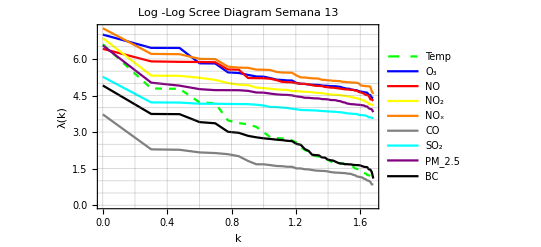

```mathematica
Clear{λFracLog,L, λLog,ScreeSSA}
L=48;

ScreeSSA[SerieT, L];
ScreeT = λLog;

ScreeSSA[Serie,L];
ScreeO3 =λLog;

ScreeSSA[SerieNO,L];
ScreeNO =λLog;

ScreeSSA[SerieNO2,L];
ScreeNO2 =λLog;

ScreeSSA[SerieNOx,L];
ScreeNOx =λLog;

ScreeSSA[SerieCO,L];
ScreeCO =λLog;

ScreeSSA[SerieSO2,L];
ScreeSO2 =λLog;

ScreeSSA[SeriePM25,L];
ScreePM25 =λLog;

ScreeSSA[SerieBC,L];
ScreeBC =λLog;

 ListLinePlot[{ScreeT, ScreeO3,ScreeNO, ScreeNO2, ScreeNOx, ScreeCO, ScreeSO2, ScreePM25, ScreeBC},Mesh->None,Frame -> True,PlotLabel->"Log -Log Scree Diagram Semana 13" ,LabelStyle->Directive[Bold,Black],PlotStyle->{{Green,Dashed},Blue,Red,Yellow,Orange, Gray, Cyan,Purple, Black},PlotLegends->{"Temp",Subscript[O,3],NO,Subscript[NO,2],Subscript[NO,x],"CO",Subscript[SO,2], Subscript[PM,2.5],"BC"},FrameLabel->{"k","λ(k)"}, GridLines->{{0,0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2}, {0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5 ,7,7.5}}]
```

```mathematica
ScreeSSA[SerieT,L];
ScreeTFrac=λFracLog;

ScreeSSA[Serie,L];
ScreeO3Frac =λFracLog;

ScreeSSA[SerieNO,L];
ScreeNOFrac =λFracLog;

ScreeSSA[SerieNO2,L];
ScreeNO2Frac =λFracLog;

ScreeSSA[SerieNOx,L];
ScreeNOxFrac =λFracLog;

ScreeSSA[SerieCO,L];
ScreeCOFrac =λFracLog;

ScreeSSA[SerieSO2,L];
ScreeSO2Frac =λFracLog;

ScreeSSA[SeriePM25,L];
ScreePM25Frac =λFracLog;

ScreeSSA[SerieBC,L];
ScreeBCFrac =λFracLog;
```

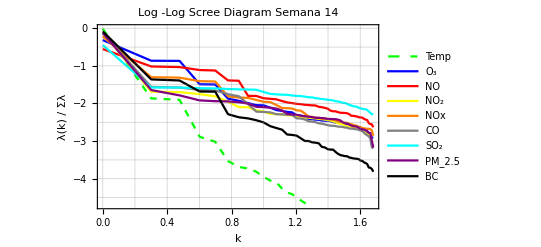

```mathematica
ListLinePlot[{ScreeTFrac,ScreeO3Frac,ScreeNOFrac, ScreeNO2Frac, ScreeNOxFrac, ScreeCOFrac, ScreeSO2Frac, ScreePM25Frac, ScreeBCFrac},Mesh->None,Frame -> True,PlotLabel->"Log -Log Scree Diagram Semana 14",LabelStyle->Directive[Bold,Black],PlotStyle->{{Green, Dashed},Blue,Red,Yellow,Orange, Gray, Cyan,Purple, Black},PlotLegends->{"Temp",Subscript[O,3],NO,Subscript[NO,2],"NOx","CO",Subscript["SO",2] , Subscript[PM,2.5],"BC"}, GridLines->{{0,0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2}, {0,-0.5,-1,-1.5,-2,-2.5,-3,-3.5,-4,-4.5,-5}},FrameLabel->{"k","λ(k) / Σλ"}]
```

□
□

“